```mathematica
Quit[]
```

```mathematica
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[1,2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}/3;
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];

r[2]=0.1  λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)Cos[k0(r[i]+r[j])];
SQ=-0.5sh ch Sum[γp[i,j](Cos[k0 r[α]]Cos[k0 r[3-α]]ρ[t].σ[i,α,β].σ[i,-α+3,β]+Cos[k0 r[α]]Cos[k0 r[3-α]]σ[i,α,β].σ[j,-α+3,β].ρ[t]-2Cos[k0 r[α]]Cos[k0 r[3-α]]σ[j,α,β].ρ[t].σ[i,-α+3,β]),{i,1,atom},{j,1,atom},{α,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,1].σ[j,α,0]+Cos[k0 r[α]]^2σ[i,α,1].σ[j,α,0].ρ[t]-2Cos[k0 r[α]]^2σ[j,α,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{α,1,2}]-0.5 sh^2Sum[γ[i,j](Cos[k0 r[α]]^2ρ[t].σ[i,α,0].σ[j,α,1]+Cos[k0 r[α]]^2σ[i,α,0].σ[j,α,1].ρ[t]-2 Cos[k0 r[α]]^2σ[j,α,1].ρ[t].σ[i,α,0]),{i,1,atom},{j,1,atom},{α,1,2}]-I Sum[Λ[i,j](Cos[k0 r[α]]Cos[k0 r[α]]σ[i,α,1].σ[j,α,0].ρ[t]-Cos[k0 r[α]]Cos[k0 r[α]]ρ[t].σ[i,α,1].σ[j,α,0]),{i,1,atom},{j,1,atom},{α,1,2}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000}];
```

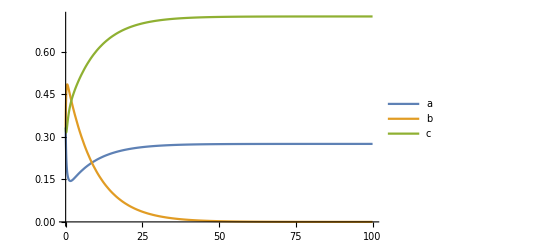

```mathematica
Plot[{a[1,1][t]/.solsq,a[2,2][t]/.solsq,a[3,3][t]/.solsq},{t,0,100},PlotLegends->{"a","b","c"}]
```

```mathematica
ρ[t]/.solsq/.t->100//MatrixForm
```

((0.275165
-5.01239×10^-18
-0.446582) | (-5.01239×10^-18
0.0000117705
5.00928×10^-18) | (-0.446582
5.00928×10^-18
0.724823))

```mathematica
({{({{0.3670987256572488}, {0.}, {-0.48201340262296405}}), ({{0.}, {2.4863924417688583*^-7}, {0.}}), ({{-0.48201340262296405}, {0.}, {00.3670987256572488}})}})
```

0.367099

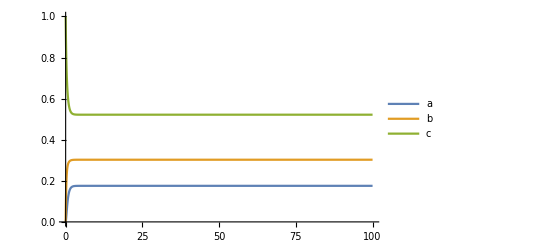

```mathematica
Plot[{a[1,1][t]/.solsq,a[2,2][t]/.solsq,a[3,3][t]/.solsq},{t,0,100},PlotLegends->{"a","b","c"}]
```

```mathematica
(*equal energy gap*)
atom=1;(*num of atoms*)
dim=3^atom;(*dimension in Hilbert space*)
σ[1,1,1]={{0, 1, 0}, {0, 0, 0}, {0, 0, 0}};(*2->1*)(*123 top to ground level*)
σ[1,1,0]={{0, 0, 0}, {1, 0, 0}, {0, 0, 0}};
σ[1,2,1]={{0, 0, 0}, {0, 0, 1}, {0, 0, 0}};
σ[1,2,0]={{0, 0, 0}, {0, 0, 0}, {0, 1, 0}};
(*[atom; transition, 1 is top, 2 it bot; +-, 1 is +, 0 is -]*)
ρ[t_]:=Table[a[i,j][t],{i,dim},{j,dim}]
slnn=Flatten[Table[a[i,j][t],{i,dim},{j,dim}]];
(*basis:a1a2a3,a1a2b3,a1b2a3,a1b2b3,b1a2a3,b1a2b3,b1b2a3,b1b2b3*)
init=DiagonalMatrix[Append[ConstantArray[0,dim-1],1]];
init={{1, 1, 1}, {1, 1, 1}, {1, 01, 1}}/3;
λ0=1;k0=2Pi/λ0;
rr=1;
sh=Sinh[rr];
ch=Cosh[rr];
r[5]=1 λ0;
r[4]=0.5λ0;
r[3]=0.5λ0;
r[2]=0.5  λ0;
r[1]=-0λ0;
Λ[i_,j_]:=(*Λ[i,j]=*)0.5Sin[k0 Abs[r[i]-r[j]] ];
γ[i_,j_]:=(*γ[i,j]=*)Cos[k0 Abs[r[j]-r[i]] ];
γp[i_,j_]:=(*γp[i,j]*)Cos[k0(r[i]+r[j])];
SQ=-0.5sh ch Sum[γp[i,j](ρ[t].σ[i,α,β].σ[i,αα,β]+σ[i,α,β].σ[j,αα,β].ρ[t]-2σ[j,α,β].ρ[t].σ[i,αα,β]),{i,1,atom},{j,1,atom},{α,1,2},{αα,1,2},{β,0,1}]-0.5(sh^2+1)Sum[γ[i,j](ρ[t].σ[i,α,1].σ[j,αα,0]+σ[i,α,1].σ[j,αα,0].ρ[t]-2σ[j,αα,0].ρ[t].σ[i,α,1]),{i,1,atom},{j,1,atom},{αα,1,2},{α,1,2}]-0.5 sh^2Sum[γ[i,j](ρ[t].σ[i,αα,0].σ[j,α,1]+σ[i,αα,0].σ[j,α,1].ρ[t]-2σ[j,α,1].ρ[t].σ[i,αα,0]),{i,1,atom},{j,1,atom},{α,1,2},{αα,1,2}]-I Sum[Λ[i,j](σ[i,α,1].σ[j,αα,0].ρ[t]-ρ[t].σ[i,α,1].σ[j,αα,0]),{i,1,atom},{j,1,atom},{α,1,2},{αα,1,2}];
solsq=NDSolve[{ρ'[t]==SQ,ρ[0]==init},slnn,{t,0,1000}];
```

```mathematica
ρ[t]/.solsq/.t->1//MatrixForm
```

((0.115262
0.201864
0.197999) | (0.201864
0.442037
0.408364) | (0.197999
0.408364
0.442702))

```mathematica
Out[137]//MatrixForm
```

((0.115262
0.0027956
0.197999) | (0.0027956
0.442037
0.0142419) | (0.197999
0.0142419
0.442702))

```mathematica
sh^2/(1.+2sh^2)
```

0.367099